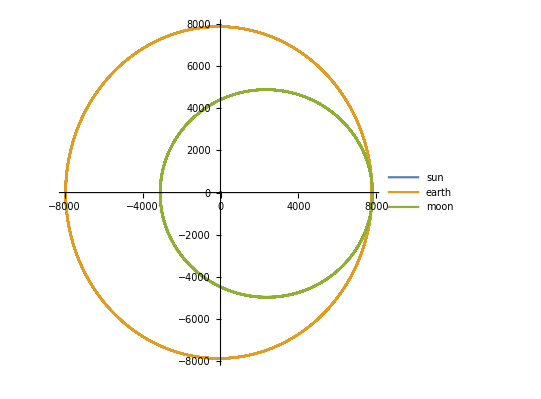

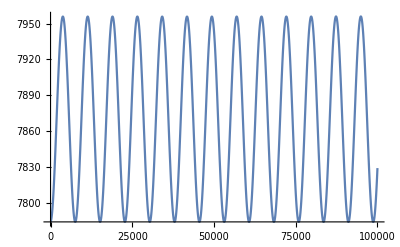

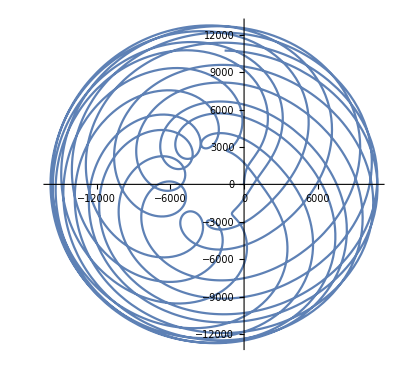

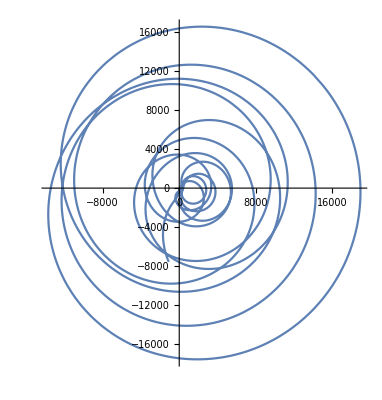

```mathematica
m1=333333; (*sun*)
m2= 1; (*earth*)
m3=0.012; (*moon*)
g=1;

r1=NDSolve[{x1''[t]==-g*m2*(x1[t]-x2[t])/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^1.5,
y1''[t]==-g*m2*(y1[t]-y2[t])/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^1.5,
x2''[t]==-g m1 *(x2[t]-x1[t])/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^1.5-g m3*(x2[t]-x3[t])/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^1.5,
y2''[t]==-g m1 *(y2[t]-y1[t])/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^1.5-g m3*(y2[t]-y3[t])/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^1.5,
x3''[t]==-g m2 *(x3[t]-x2[t])/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^1.5-g m1*(x3[t]-x1[t])/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^1.5,
y3''[t]==-g m2 *(y3[t]-y1[t])/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^1.5-g m1*(y3[t]-y1[t])/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^1.5,
x1[0]==0,
y1[0]==0,
x1'[0]==0,
y1'[0]==0,
x2[0]==7784,
y2[0]==0,
x2'[0]==0,
y2'[0]==6.58,
x3[0]==x2[0]+19.7,
y3[0]==0,
x3'[0]==0,
y3'[0]==y2'[0]+0.225
},{x1,y1, x2, y2,x3,y3},{t,0,100000}];

sunx=x1/.First[r1];
suny=y1/.First[r1];
earthx=x2/.First[r1];
earthy=y2/.First[r1];
moonx=x3/.First[r1];
moony=y3/.First[r1];

ParametricPlot[{{sunx[t],suny[t]},{earthx[t],earthy[t]},{moonx[t],moony[t]}},{t,0,100000}(*,PlotRange->{{-2,2},{0,4}}*), PlotLegends->{"sun", "earth","moon"}]
Plot[(earthx[t]^2+earthy[t]^2)^(1/2),{t,0,100000}]
ParametricPlot[{earthx[t]-moonx[t],earthy[t]-moony[t]},{t,0,100000}]
```

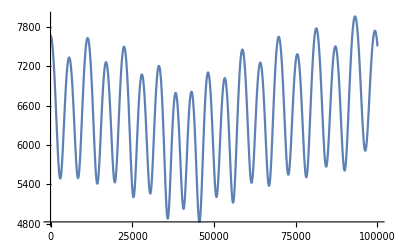

```mathematica
Plot[(earthx[t]^2+earthy[t]^2)^(1/2),{t,0,100000}]
```